```mathematica
(*<<peeters`;
peeters`setGitDir["../tmp"]*)
```

Get::noopen: Cannot open peeters`.

peeters`setGitDir[../tmp]

```mathematica
ClearAll[alpha, beta, a,b]
```

```mathematica
SetDirectory["~/tmp"];
data=Import["data.json"];
```

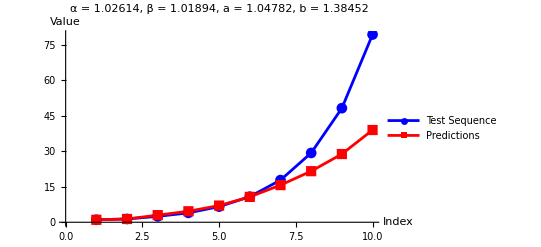

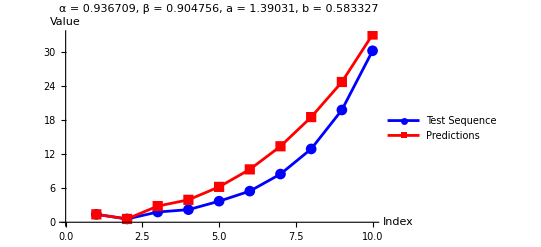

-Graphics-

p2.png

p3.png

p_all.png

```mathematica
ClearAll[plotOnePair]
plotOnePair[element_]:=Module[{test,pred,alpha,beta,a,b},
a=Lookup[element,"a"];
b=Lookup[element,"b"];
alpha=Lookup[element,"alpha"];
beta=Lookup[element,"beta"];
test=Lookup[element,"test_sequence"];
pred=Lookup[element,"predictions"];

ListLinePlot[{test,pred},
PlotLegends->{"Test Sequence","Predictions"},PlotLabel->StringForm["α = ``, β = ``, a = ``, b = ``",alpha,beta, a, b],
AxesLabel->{"Index","Value"},
PlotMarkers->Automatic,
PlotStyle->{Blue,Red}(*,
ImageSize->Medium]*)
]
]

ClearAll[p2, p3, pall]
p2 = plotOnePair[data[[2]]]
p3  = plotOnePair[data[[3]]]
pall = GraphicsGrid[Partition[plotOnePair[#]&/@ data,UpTo[4]]]
```

```mathematica
Export["p2.jpeg", p2]
Export["p3.jpeg", p3]
Export["p_all.jpeg", pall]
```

p2.jpeg

p3.jpeg

p_all.jpeg